```mathematica
f=3x^2+4 x y -3 x ;               (* x' *)
g=4y^2+3 x y -4y;               (* y' *)

s=Solve[{f==0, g==0}, {x,y}];
TableForm[s]                                (* critical points *)


a=RegionPlot[-1+x+(4*y)/3 <-(1/3), {x, 0, 1}, {y,0 ,1},PlotStyle->RGBColor[1,0.85,0.69], BoundaryStyle->None];       (* region with accelerated expansion *)

b=StreamPlot[{f,g},{x,0,1},{y,0,1},PlotTheme->"Monochrome",StreamPoints->Fine,StreamStyle->GrayLevel[0.85],PlotRange->All];
c={Text["A",{0.04,0.01},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["B",{0.04,0.99},BaseStyle->{FontSize->22, Bold,FontFamily->"Times",Italic}],Text["C",{0.96,0.01},BaseStyle->{FontSize->22, Bold,FontFamily->"Times",Italic}]};

Show[a,b, Graphics[c],Epilog->{RGBColor[0,0,0],PointSize[0.03],Point[{x,y}/. s]}, FrameLabel->{Style[HoldForm[x],FontFamily->"Times",FontSize->22],
Style[HoldForm[Rotate["y", -Pi/2]],FontFamily->"Times",FontSize->22]}, ImageSize->Large, Frame->True, Axes->False , FrameStyle->Directive[Black,Thick], BaseStyle->{FontSize->15},BaseStyle->{FontFamily->"Times",FontSize->16}]
```

x→0 | y→1
x→1 | y→0
x→0 | y→0

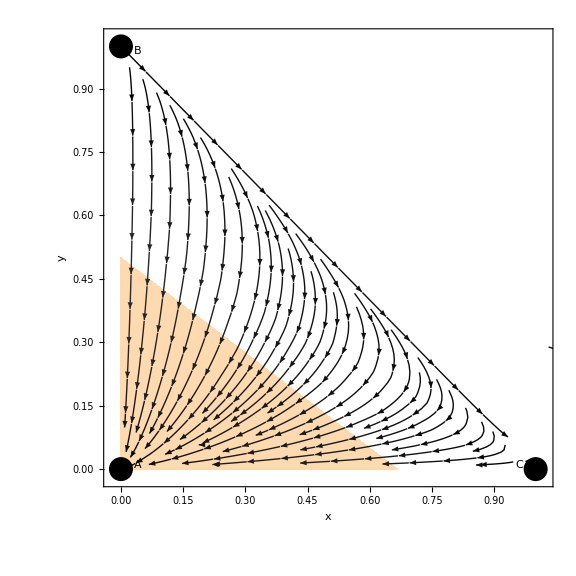

```mathematica
jacobian={{6x+4y-3,4x},{3y, 3x+8y-4}};
MatrixForm[jacobian]

v00={x->0, y->0}
e00=Eigenvalues[jacobian]/.v00
MatrixForm[jacobian]/.v00

v10={x->1, y->0}
e10=Eigenvalues[jacobian]/.v10
MatrixForm[jacobian]/.v10

v01={x->0, y->1}
e01=Eigenvalues[jacobian]/.v01
MatrixForm[jacobian]/.v01
```

(-3+6 x+4 y | 4 x
3 y | -4+3 x+8 y)

{x→0,y→0}

{-4,-3}

(-3 | 0
0 | -4)

{x→1,y→0}

{-1,3}

(3 | 4
0 | -1)

{x→0,y→1}

{1,4}

(1 | 0
3 | 4)